# MCMC:HW2

Qi Chen(qc586)

## Problem 1

A chain with transition matrix P and stationary density π is reversible if

π_i p_(i j)=π_j p_(j i)

for all i,j. Show that this condition is satisfied for the P with elements

p_(i j)=α_(i j)q_(i j)+(1-r_i)1(i=j)

where 1(i=j) if i=j and is 0 otherwise, and

α_(i j)=min{1,(π_j q_(j i))/(π_i q_(i j))}

and

r_i=(∑_(j=1))^k α_(i j)q_(i j)

Here (q_(i j))_(j=1)^k are a set of weights for each i.

Solution:

π_i p_(i j)=π_i[α_(i j)q_(i j)+(1-r_i)1(i=j)]
=α_(i j)π_i q_(i j)+π_i(1-(∑_(l=1))^k α_(i l)q_(i l))1(i=j)
=min{1,(π_j q_(j i))/(π_i q_(i j))}π_i q_(i j)+π_i(1-(∑_(l=1))^k α_(i l)q_(i l))1(i=j)
=min{π_i q_(i j),π_j q_(j i)}+(π_i-(∑_(l=1))^k min{1,(π_l q_(l i))/(π_i q_(i l))}π_i q_(i l))1(i=j)
=min{π_i q_(i j),π_j q_(j i)}+(π_i-(∑_(l=1))^k min{π_i q_(i l),π_l q_(l i)})1(i=j)

On the other hand, by exchanging i and j in the above expression, one finds

π_j p_(j i)=min{π_j q_(j i),π_i q_(i j)}+(π_j-(∑_(l=1))^k min{π_j q_(j l),π_l q_(l j)})1(i=j)
=min{π_j q_(j i),π_i q_(i j)}+(π_i-(∑_(l=1))^k min{π_i q_(i l),π_l q_(l i)})1(i=j)
=π_i p_(i j)

## Problem 2

Suppose that the joint density f(x,q) is given by

f(x,q)=(q^x(1−q))^(1-x),x∈{0,1} and 0<q<1.

Consider the transition density, with X_n, X_(n+1)∈ {0, 1},

p(X_(n+1)|X_n)=2∫_0^1 (q^(X_n+X_(n+1))(1-q))^(2-X_n-X_(n+1))ⅆq

Find the stationary density for this transition density. Generate the sequence (X_n), starting with P(X_0 = 1) = 1/2, and use this to confirm your finding on the stationary density.

Solution: According to the definition of the stationary condition,

f(X_(n+1))=∑_X_n P(X_(n+1)|X_n)f(X_n)

From Eq. (DisplayFormulaNumbered), one can obtain the marginal density of x as

f(x)=∫_0^1 f(x,q)ⅆq=(Γ(1+x)Γ(2-x))/(Γ(3))=(x!(1-x)!)/2,x∈{0,1}

Then

∑_X_n P(X_(n+1)|X_n)f(X_n)=∑_X_n (X_n!(1-X_n)!)/2 2∫_0^1 (q'^(X_n+X_(n+1))(1-q'))^(2-X_n-X_(n+1))ⅆ q'
=∑_X_n X_n!(1-X_n)!(Γ(1+X_n+X_(n+1))Γ(3-X_n-X_(n+1)))/(Γ(4))
=(Γ(1+X_(n+1))Γ(3-X_(n+1)))/(Γ(4))+(Γ(2+X_(n+1))Γ(2-X_(n+1)))/(Γ(4))
=(Γ(1+X_(n+1))(2-X_(n+1))Γ(2-X_(n+1)))/(Γ(4))+((1+X_(n+1))Γ(1+X_(n+1))Γ(2-X_(n+1)))/(Γ(4))
=(2-X_(n+1)+1+X_(n+1))/(Γ(4))Γ(1+X_(n+1))Γ(2-X_(n+1))
=(Γ(1+X_(n+1))Γ(2-X_(n+1)))/2
=(X_(n+1)!(1-X_(n+1))!)/2,X_(n+1)∈{0,1}=f(X_(n+1))

So we have verified that the stationary density for this transition is just

f(x)=1/2,x∈{0,1}

```mathematica
Integrate[x^n(1-x)^m,{x,0,1},Assumptions->{m∈Integers,n∈Integers}]
```

ConditionalExpression[(Gamma[1+m] Gamma[1+n])/Gamma[2+m+n],n≥0&&m≥0]

The Markov chain is discrete and we can write

P(X_(n+1)=j|X_n=i)=p_(i j)=2 (Γ(1+i+j)Γ(3-i-j))/(Γ(4))=((i+j)!(2-i-j)!)/3

f(X_(n+1)=j)=f_j

In matrix notation,

P=(2/3 | 1/3
1/3 | 2/3),f=(1/2
1/2)

f_j=∑_(i=0,1) f_i p_(i j)

The simulation results are given in the following histogram (P_0(X=i)=1/2):

-Graphics-

## Problem 3

Consider the integral

I=∫_(-∞)^∞ 1/(1+x^4)ⅇ^(-1/2 x^2)ⅆx

Evaluate this integral using a Markov chain sample (X_n) given by X_(n+1)~N(ρ X_n,1−ρ^2). What is the best ρ to use in this case and demonstrate via simulation.

```mathematica
NIntegrate[1/(1+x^4)Exp[-1/2 x^2],{x,-∞,∞}]
```

1.69639

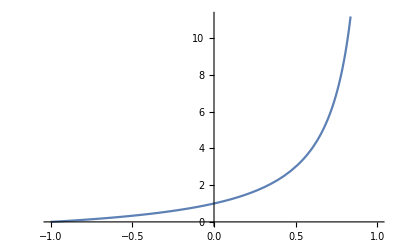

```mathematica
Plot[(1+x)/(1-x),{x,-1,1}]
```

Solution: The approximate value of the integral is

I=∫_(-∞)^∞ 1/(1+x^4)ⅇ^(-1/2 x^2)ⅆx≈1.69639

The MCMC simulation can be performed based on the following form:

I=∫_(-∞)^∞ g(x)f(x)ⅆx

where

f(x)=1/(√(2π))ⅇ^(-1/2 x^2)

g(x)=(√(2π))/(1+x^4)

The convergence and the variance plots are as follows

-Graphics-

-Graphics-

The simulation results gives

I≈I_N=1/N(∑_(i=1))^N g(x_i)≈1.692704

The best ρ to choose can be derived from minimization of variance:

σ^2=Var(g(X_1))+2(∑_(i=1))^∞Cov(g(X_1),g(X_i))

If we plot the sample variance of size m=100 integral results

S^2=1/(m-1)(∑_(i=1))^m(I_N^i-(Ī)_N)^2

One finds ρ=0 is the minimum. This is the case when X_1,…,X_n are i.i.d. N(0,1) and MCMC sampling is the same as the importance sampling.

# Appendix: R-code

# problem 2
n<-1000
x<-array(dim=n)
# initialize
x[1]<-sample(0:1, 1, replace = TRUE)
for(i in 2:n){
  x[i]<-sample(c(0,1), 1, replace = TRUE, prob=c(factorial(x[i-1])*factorial(2-x[i-1])/3,factorial(1+x[i-1])*factorial(1-x[i-1])/3))
}
hist(x)

# problem 3
n<-5000
x<-array(dim=n)
x[1] <- rnorm(1, 0, 1)
rho <- 0
for(i in 2:n){
  x[i]<-rnorm(1, rho*x[i-1], sqrt(1-rho**2))
}
g <- sqrt(2*pi)/(1+x**4)
I <- sum(g)/n
I

I_N_rho <- function(n,rho,x1){
  x<-array(dim=n)
  x[1] <- x1
  for(i in 2:n){
    x[i]<-rnorm(1, rho*x[i-1], sqrt(1-rho**2))
  }
  g <- sqrt(2*pi)/(1+x**4)
  return(sum(g)/n)
}

I_N <- function(n){
  return(I_N_rho(n,rho,rnorm(1, 0, 1)))
}

var_rho <- function(rho){
  g <-array(dim=1000)
  for(i in 1:1000){
    g[i] <- I_N_rho(1000,rho,rnorm(1, 0, 1))
  }
   return(sum((g-mean(g))**2)/(1000-1))
}

n = 100:2000
results1 <- lapply(n,I_N)
plot(n, results1)

m=100
rho=seq(from=-1, to=1,length.out=m)
variance <- lapply(rho,var_rho)
plot(rho, variance, ylim=c(0.000, 0.01))